0.71

1

MittagLefflerE[0.71,(0.-1. ⅈ) x^0.71]+MittagLefflerE[0.71,(0.+1. ⅈ) x^0.71]

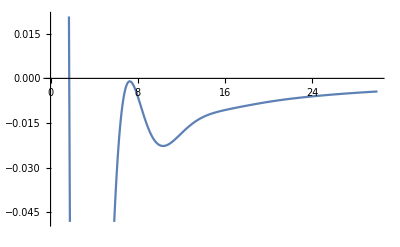

```mathematica
Clear[a,k,n,x]

a = 0.71
k = 1
psi = MittagLefflerE[a,I k^a x^a]+MittagLefflerE[a,-I k^a x^a]
Plot[psi,{x,0,30}]
```